```mathematica
dir=NotebookDirectory[];
SetDirectory[dir];
```

```mathematica
jet[u_?NumericQ]:=Blend[{{0,RGBColor[0,0,9/16]},{1/9,Blue},{23/63,Cyan},{13/21,Yellow},{47/63,Orange},{55/63,Red},{1,RGBColor[1/2,0,0]}},u]/;0≤u≤1;
```

### List of constants

```mathematica
EH=39.9;(*Hartree in meV*)
aB=3.17;(*Bohr radius in nm*)
Eshift=10;(*energy shift*)
numE=1;(*number of eigenenergies to be solved for*)
r0=5; (*scale radius*)
rc=0.2;
Uc=0.417;
γ=0.208;(*effective mass ratio*)
maxcell=10^-4; (*maximum volume of the finite elements (relative to the volume of the total domain)*)
αmax=π/2.1;
pres=3;
```

### Schrodinger equation and boundary conditions

```mathematica
U[r_]=Uc/(4π rc^3/3)HeavisideTheta[rc-r];
```

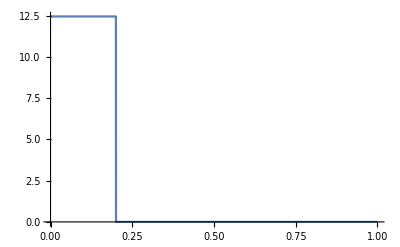

```mathematica
Plot[U[r],{r,0,1},Exclusions->None]
```

```mathematica
PDE0=-(1/2)D[f[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f[r,θ],θ]- 1/(2 r^2)D[f[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))+m^2/(2 r^2(Sin[θ])^2)-Wn) f[r,θ];
```

```mathematica
PDEc=-(1/2)D[f[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f[r,θ],θ]- 1/(2 r^2)D[f[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))-U[r]+m^2/(2 r^2(Sin[θ])^2)-Wn) f[r,θ];
```

```mathematica
PDE1=-(1/2)D[f1[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f1[r,θ],θ]- 1/(2 r^2)D[f1[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))- U[r]/3 KroneckerDelta[m,0]+m^2/(2 r^2(Sin[θ])^2)-Wn) f1[r,θ]-2 U[r]/3 KroneckerDelta[m,0]f2[r,θ];
PDE2=-(1/2)D[f2[r,θ],{r,2}]-1/(2 r^2(Tan[θ]))D[f2[r,θ],θ]- 1/(2 r^2)D[f2[r,θ],{θ,2}]+(-1/(r √(1-(1-γ)(Cos[θ])^2))-2 U[r]/3 KroneckerDelta[m,0]+m^2/(2 r^2(Sin[θ])^2)-Wn) f2[r,θ]-U[r]/3 KroneckerDelta[m,0]f1[r,θ];
```

```mathematica
PDEctn=Simplify[PDEc/. f-> (F[ArcTan[#1/r0],#2]&)/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ; (* transform to tangent space r = r0 tan[αr] to map [0, ∞] in r to [0, π/2] in αr*)
PDE0tn=Simplify[PDE0/. f-> (F[ArcTan[#1/r0],#2]&)/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ;
PDE1tn=Simplify[PDE1/. {f1-> (F1[ArcTan[#1/r0],#2]&),f2-> (F2[ArcTan[#1/r0],#2]&)}/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ; 
PDE2tn=Simplify[PDE2/. {f1-> (F1[ArcTan[#1/r0],#2]&),f2-> (F2[ArcTan[#1/r0],#2]&)}/.{r->(r0 Tan[αr])},{Pi/2>αr>0}] ;
```

```mathematica
Ω=ImplicitRegion[True,{{αr,0,αmax},{θ,0,Pi/2}}];
```

```mathematica
Γs=DirichletCondition[F[αr,θ]==0,αr==0||αr==αmax];(*boundary condition for even functions in θ'=π/2-θ*)
Γa=DirichletCondition[F[αr,θ]==0,αr==0||αr==αmax||θ==Pi/2]; 
Γ1s=DirichletCondition[F1[αr,θ]==0,αr==0||αr==αmax];(*boundary condition for even functions in θ'=π/2-θ*)
Γ1a=DirichletCondition[F1[αr,θ]==0,αr==0||αr==αmax||θ==Pi/2]; 
Γ2s=DirichletCondition[F2[αr,θ]==0,αr==0||αr==αmax];(*boundary condition for even functions in θ'=π/2-θ*)
Γ2a=DirichletCondition[F2[αr,θ]==0,αr==0||αr==αmax||θ==Pi/2]; (*boundary condition for odd functions in θ'=π/2-θ*)
```

m=0 even parity states

```mathematica
{E0e,f0e}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->0,Wn-> 0},Γs},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E0e=E0e-Eshift
```

{-1.14108}

m=0 odd parity states

```mathematica
{E0o,f0o}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->0,Wn-> 0},Γa},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E0o=E0o-Eshift
```

{-0.288233}

```mathematica
(E0o[[1]]-E0e[[1]])/3
```

0.284284

```mathematica
0.2842838621475335*39.9
```

11.3429

m0=1 odd parity states

```mathematica
{E1o,f1o}=NDEigensystem[{PDEctn+Eshift F[αr,θ]/.{m->1,Wn-> 0},Γs},F[αr,θ],{αr,θ}∈Ω,numE,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->maxcell}}},"Eigensystem"->{"Arnoldi","MaxIterations"->40000,"Criteria"-> "RealPart" }}];
```

```mathematica
E1o=E1o-Eshift
```

{-0.16054}

```mathematica
(E1o[[1]]-E0e[[1]])/3
```

0.326848

```mathematica
0.32684812707477917*39.9
```

13.0412

### Normalization

```mathematica
N0e=ConstantArray[0,numE];
```

```mathematica
For[k=1,k<numE+1,k++,
N0e[[k]]=NIntegrate[(f0e[[k]])^2 r0 (Sec[αr])^2 Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->6,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

### Chi 3 calculation

```mathematica
ω=0.1; (*light frequency*)
```

```mathematica
W[x_]=x+E0e[[1]];
```

### 1st intermediate state

```mathematica
sols1101=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] f0e[[1]]/.{m->0,Wn-> W[ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g1101[αr_,θ_]=sols1101[[1,1,2]][αr,θ];
```

```mathematica
sols1112=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] f0e[[1]]/2/.{m->1,Wn->  W[ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g1112[αr_,θ_]=sols1112[[1,1,2]][αr,θ];
```

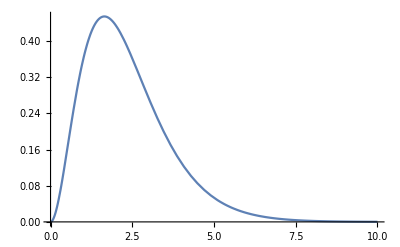

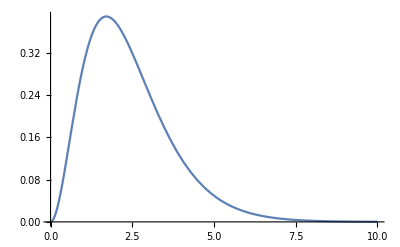

```mathematica
Plot[g1101[ArcTan[r/r0],π/4],{r,0,10},PlotRange->All]
Plot[g1112[ArcTan[r/r0],π/4],{r,0,10},PlotRange->All]
```

```mathematica
sols4101=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] f0e[[1]]/.{m->0,Wn-> W[-3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g4101[αr_,θ_]=sols4101[[1,1,2]][αr,θ];
```

```mathematica
sols4112=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] f0e[[1]]/2/.{m->1,Wn->  W[-3ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g4112[αr_,θ_]=sols4112[[1,1,2]][αr,θ];
```

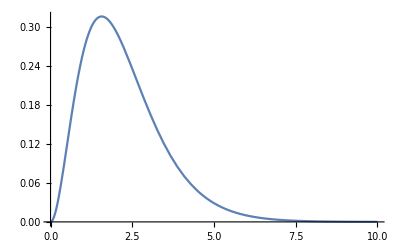

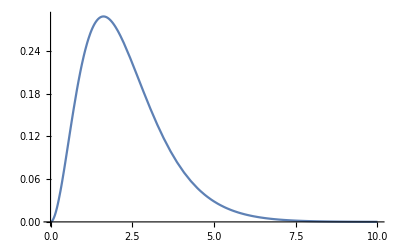

```mathematica
Plot[g4101[ArcTan[r/r0],π/4],{r,0,10},PlotRange->All]
Plot[g4112[ArcTan[r/r0],π/4],{r,0,10},PlotRange->All]
```

### 2nd intermediate state

```mathematica
sols120=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g1101[αr,θ]/.{m->0,Wn->  W[2ω]},PDE2tn==r0 Tan[αr]Sin[θ]g1112[αr,θ]/.{m->0,Wn->  W[2ω]}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g1201[αr_,θ_]=sols120[[1,1,2]][αr,θ];
g1202[αr_,θ_]=sols120[[1,2,2]][αr,θ];
```

```mathematica
sols1222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g1112[αr,θ]/2/.{m->2,Wn->  W[2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g1222[αr_,θ_]=sols1222[[1,1,2]][αr,θ];
```

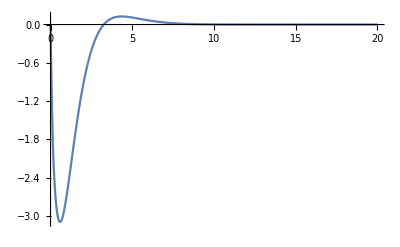

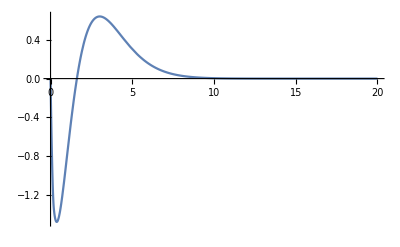

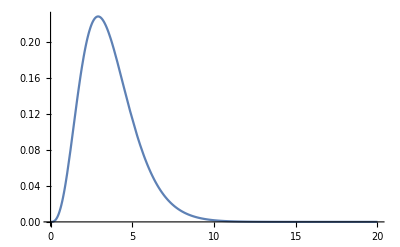

```mathematica
Plot[g1201[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g1202[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g1222[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
```

```mathematica
sols320=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g1101[αr,θ]/.{m->0,Wn->  W[-2ω]},PDE2tn==r0 Tan[αr]Sin[θ]g1112[αr,θ]/.{m->0,Wn->  W[-2ω]}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g3201[αr_,θ_]=sols320[[1,1,2]][αr,θ];
g3202[αr_,θ_]=sols320[[1,2,2]][αr,θ];
```

```mathematica
sols3222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g1112[αr,θ]/2/.{m->2,Wn->  W[-2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g3222[αr_,θ_]=sols3222[[1,1,2]][αr,θ];
```

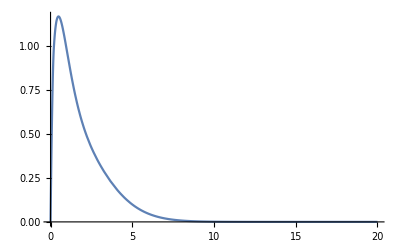

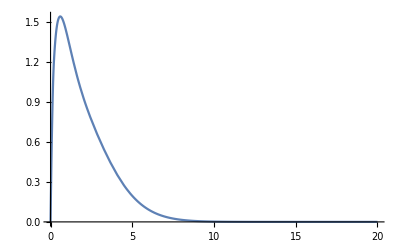

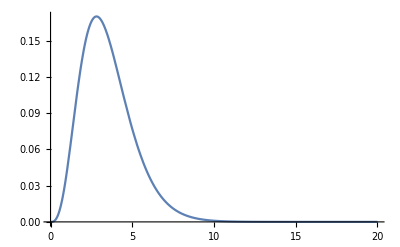

```mathematica
Plot[g3201[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g3202[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g3222[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
```

```mathematica
sols420=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g4101[αr,θ]/.{m->0,Wn->  W[-2ω]},PDE2tn==r0 Tan[αr]Sin[θ]g4112[αr,θ]/.{m->0,Wn->  W[-2ω]}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g4201[αr_,θ_]=sols420[[1,1,2]][αr,θ];
g4202[αr_,θ_]=sols420[[1,2,2]][αr,θ];
```

```mathematica
sols4222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g4112[αr,θ]/2/.{m->2,Wn->  W[-2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g4222[αr_,θ_]=sols4222[[1,1,2]][αr,θ];
```

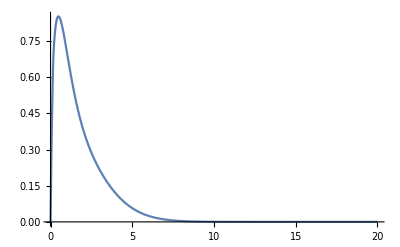

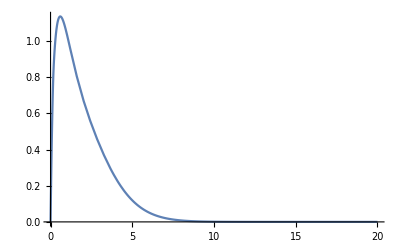

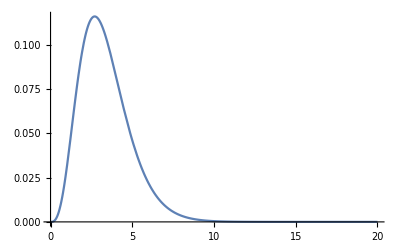

```mathematica
Plot[g4201[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g4202[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g4222[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
```

### 3rd intermediate state

```mathematica
sols1301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g1201[αr,θ]/.{m->0,Wn->  W[3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g1301[αr_,θ_]=sols1301[[1,1,2]][αr,θ];
```

```mathematica
sols1312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g1202[αr,θ]+g1222[αr,θ])/2/.{m->1,Wn->  W[3ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g1312[αr_,θ_]=sols1312[[1,1,2]][αr,θ];
```

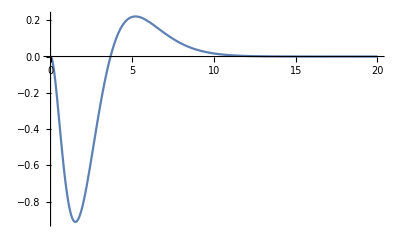

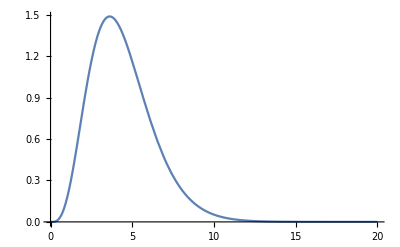

```mathematica
Plot[g1301[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g1312[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
```

```mathematica
sols1301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g1201[αr,θ]/.{m->0,Wn->  W[3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g1301[αr_,θ_]=sols1301[[1,1,2]][αr,θ];
```

```mathematica
sols1312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g1202[αr,θ]+g1222[αr,θ])/2/.{m->1,Wn->  W[3ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g1312[αr_,θ_]=sols1312[[1,1,2]][αr,θ];
```

```mathematica
Plot[g1301[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g1312[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
sols2301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g1201[αr,θ]/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g2301[αr_,θ_]=sols2301[[1,1,2]][αr,θ];
```

```mathematica
sols2312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g1202[αr,θ]+g1222[αr,θ])/2/.{m->1,Wn->  W[-ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g2312[αr_,θ_]=sols2312[[1,1,2]][αr,θ];
```

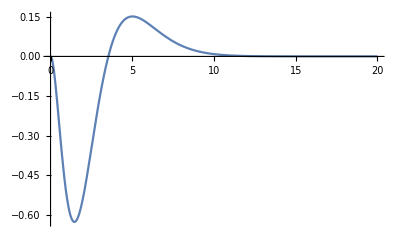

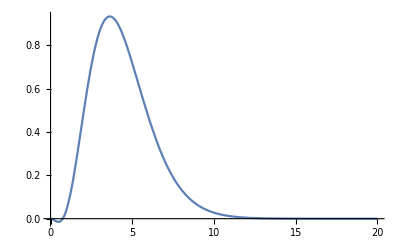

```mathematica
Plot[g2301[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g2312[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
```

```mathematica
sols3301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g3201[αr,θ]/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g3301[αr_,θ_]=sols3301[[1,1,2]][αr,θ];
```

```mathematica
sols3312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g3202[αr,θ]+g3222[αr,θ])/2/.{m->1,Wn->  W[-ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g3312[αr_,θ_]=sols3312[[1,1,2]][αr,θ];
```

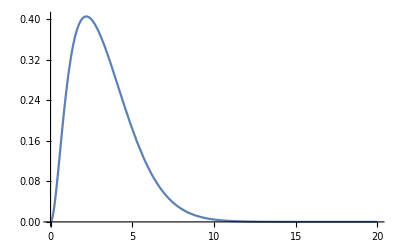

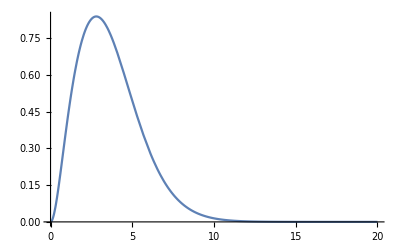

```mathematica
Plot[g3301[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g3312[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
```

```mathematica
sols4301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g4201[αr,θ]/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g4301[αr_,θ_]=sols4301[[1,1,2]][αr,θ];
```

```mathematica
sols4312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g4202[αr,θ]+g4222[αr,θ])/2/.{m->1,Wn->  W[-ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
```

```mathematica
g4312[αr_,θ_]=sols4312[[1,1,2]][αr,θ];
```

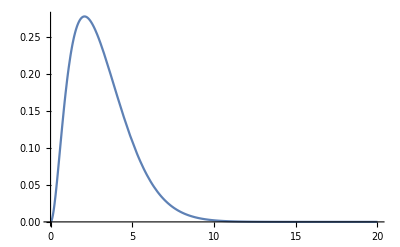

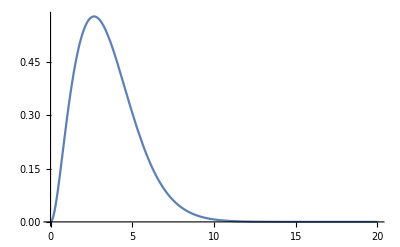

```mathematica
Plot[g4301[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
Plot[g4312[ArcTan[r/r0],π/4],{r,0,20},PlotRange->All]
```

### chi3 integral

```mathematica
χ31=1/3(√γ)/N0e[[1]] NIntegrate[f0e[[1]]g1301[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 2/3 1/N0e[[1]] NIntegrate[f0e[[1]]g1312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
```

```mathematica
χ32=1/3(√γ)/N0e[[1]] NIntegrate[f0e[[1]]g2301[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 2/3 1/N0e[[1]] NIntegrate[f0e[[1]]g2312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
```

```mathematica
χ33=1/3(√γ)/N0e[[1]] NIntegrate[f0e[[1]]g3301[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 2/3 1/N0e[[1]] NIntegrate[f0e[[1]]g3312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
```

```mathematica
χ34=1/3(√γ)/N0e[[1]] NIntegrate[f0e[[1]]g4301[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 2/3 1/N0e[[1]] NIntegrate[f0e[[1]]g4312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
```

```mathematica
χ3=χ31+χ32+χ33+χ34
```

1.29259

### Chi3 spectrum

```mathematica
ωmin=0;
ωmax=-0.99E0e[[1]]/3;
```

```mathematica
ωL=Range[ωmin,ωmax,(ωmax-ωmin)/1000];
χ3L1=ConstantArray[0,{Length[ωL]}];
χ3L2=ConstantArray[0,{Length[ωL]}];
χ3L3=ConstantArray[0,{Length[ωL]}];
χ3L4=ConstantArray[0,{Length[ωL]}];
χ3L=ConstantArray[0,{Length[ωL]}];
```

```mathematica
For[k=1,k<Length[ωL]+1,k++,
Print[k];
ω=ωL[[k]];
sols1101=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] f0e[[1]]/.{m->0,Wn-> W[ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1101[αr_,θ_]=sols1101[[1,1,2]][αr,θ];
sols1112=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] f0e[[1]]/2/.{m->1,Wn->  W[ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1112[αr_,θ_]=sols1112[[1,1,2]][αr,θ];
sols4101=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] f0e[[1]]/.{m->0,Wn-> W[-3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4101[αr_,θ_]=sols4101[[1,1,2]][αr,θ];
sols4112=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] f0e[[1]]/2/.{m->1,Wn->  W[-3ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4112[αr_,θ_]=sols4112[[1,1,2]][αr,θ];
sols120=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g1101[αr,θ]/.{m->0,Wn->  W[2ω]},PDE2tn==r0 Tan[αr]Sin[θ]g1112[αr,θ]/.{m->0,Wn->  W[2ω]}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1201[αr_,θ_]=sols120[[1,1,2]][αr,θ];
g1202[αr_,θ_]=sols120[[1,2,2]][αr,θ];
sols1222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g1112[αr,θ]/2/.{m->2,Wn->  W[2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1222[αr_,θ_]=sols1222[[1,1,2]][αr,θ];
sols320=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g1101[αr,θ]/.{m->0,Wn->  W[-2ω]},PDE2tn==r0 Tan[αr]Sin[θ]g1112[αr,θ]/.{m->0,Wn->  W[-2ω]}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3201[αr_,θ_]=sols320[[1,1,2]][αr,θ];
g3202[αr_,θ_]=sols320[[1,2,2]][αr,θ];
sols3222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g1112[αr,θ]/2/.{m->2,Wn->  W[-2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3222[αr_,θ_]=sols3222[[1,1,2]][αr,θ];
sols420=NDSolve[{{PDE1tn==√γ r0 Tan[αr]Cos[θ]g4101[αr,θ]/.{m->0,Wn->  W[-2ω]},PDE2tn==r0 Tan[αr]Sin[θ]g4112[αr,θ]/.{m->0,Wn->  W[-2ω]}},{Γ1s,Γ2s}},{F1,F2},{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4201[αr_,θ_]=sols420[[1,1,2]][αr,θ];
g4202[αr_,θ_]=sols420[[1,2,2]][αr,θ];
sols4222=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] g4112[αr,θ]/2/.{m->2,Wn->  W[-2ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4222[αr_,θ_]=sols4222[[1,1,2]][αr,θ];
sols1301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g1201[αr,θ]/.{m->0,Wn->  W[3ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1301[αr_,θ_]=sols1301[[1,1,2]][αr,θ];
sols1312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g1202[αr,θ]+g1222[αr,θ])/2/.{m->1,Wn->  W[3ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g1312[αr_,θ_]=sols1312[[1,1,2]][αr,θ];
sols2301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g1201[αr,θ]/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g2301[αr_,θ_]=sols2301[[1,1,2]][αr,θ];
sols2312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g1202[αr,θ]+g1222[αr,θ])/2/.{m->1,Wn->  W[-ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g2312[αr_,θ_]=sols2312[[1,1,2]][αr,θ];
sols3301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g3201[αr,θ]/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3301[αr_,θ_]=sols3301[[1,1,2]][αr,θ];
sols3312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g3202[αr,θ]+g3222[αr,θ])/2/.{m->1,Wn->  W[-ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g3312[αr_,θ_]=sols3312[[1,1,2]][αr,θ];
sols4301=NDSolve[{PDE0tn==√γ r0 Tan[αr]Cos[θ] g4201[αr,θ]/.{m->0,Wn->  W[-ω]},Γa},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4301[αr_,θ_]=sols4301[[1,1,2]][αr,θ];
sols4312=NDSolve[{PDE0tn==r0 Tan[αr]Sin[θ] (g4202[αr,θ]+g4222[αr,θ])/2/.{m->1,Wn->  W[-ω]},Γs},F,{αr,θ}∈Ω,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcell},"IntegrationOrder"->5}}];
g4312[αr_,θ_]=sols4312[[1,1,2]][αr,θ];
χ3L1[[k]]=1/3(√γ)/N0e[[1]] NIntegrate[f0e[[1]]g1301[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 2/3 1/N0e[[1]] NIntegrate[f0e[[1]]g1312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
χ3L2[[k]]=1/3(√γ)/N0e[[1]] NIntegrate[f0e[[1]]g2301[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 2/3 1/N0e[[1]] NIntegrate[f0e[[1]]g2312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
χ3L3[[k]]=1/3(√γ)/N0e[[1]] NIntegrate[f0e[[1]]g3301[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 2/3 1/N0e[[1]] NIntegrate[f0e[[1]]g3312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
χ3L4[[k]]=1/3(√γ)/N0e[[1]] NIntegrate[f0e[[1]]g4301[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Cos[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal-> pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}]+ 2/3 1/N0e[[1]] NIntegrate[f0e[[1]]g4312[αr,θ]r0 Tan[αr]r0 (Sec[αr])^2 Sin[θ] Sin[θ],{θ,0,π/2},{αr,0,αmax},PrecisionGoal->pres,Method->{"GlobalAdaptive","MaxErrorIncreases"-> 20000}];
χ3L[[k]]=χ3L1[[k]]+χ3L2[[k]]+χ3L3[[k]]+χ3L4[[k]];]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

110

111

112

113

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

501

502

503

504

505

506

507

508

509

510

511

512

513

514

515

516

517

518

519

520

521

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

522

523

524

525

526

527

528

529

530

531

532

533

534

535

536

537

538

539

540

541

542

543

544

545

546

547

548

549

550

551

552

553

554

555

556

557

558

559

560

561

562

563

564

565

566

567

568

569

570

571

572

573

574

575

576

577

578

579

580

581

582

583

584

585

586

587

588

589

590

591

592

593

594

595

596

597

598

599

600

601

602

603

604

605

606

607

608

609

610

611

612

613

614

615

616

617

618

619

620

621

622

623

624

625

626

627

628

629

630

631

632

633

634

635

636

637

638

639

640

641

642

643

644

645

646

647

648

649

650

651

652

653

654

655

656

657

658

659

660

661

662

663

664

665

666

667

668

669

670

671

672

673

674

675

676

677

678

679

680

681

682

683

684

685

686

687

688

689

690

691

692

693

694

695

696

697

698

699

700

701

702

703

704

705

706

707

708

709

710

711

712

713

714

715

716

717

718

719

720

721

722

723

724

725

726

727

728

729

730

731

732

733

734

735

736

737

738

739

740

741

742

743

744

745

746

747

748

749

750

751

752

753

754

755

756

757

758

759

760

761

762

763

764

765

766

767

768

769

770

771

772

773

774

775

776

777

778

779

780

781

782

783

784

785

786

787

788

789

790

791

792

793

794

795

796

797

798

799

800

801

802

803

804

805

806

807

808

809

810

811

812

813

814

815

816

817

818

819

820

821

822

823

824

825

826

827

828

829

830

831

832

833

834

835

836

837

838

839

840

841

842

843

844

845

846

847

848

849

850

851

852

853

854

855

856

857

858

859

860

861

862

863

864

865

866

867

868

869

870

871

872

873

874

875

876

877

878

879

880

881

882

883

884

885

886

887

888

889

890

891

892

893

894

895

896

897

898

899

900

901

902

903

904

905

906

907

908

909

910

911

912

913

914

915

916

917

918

919

920

921

922

923

924

925

926

927

928

929

930

931

932

933

934

935

936

937

938

939

940

941

942

943

944

945

946

947

948

949

950

951

952

953

954

955

956

957

958

959

960

961

962

963

964

965

966

967

968

969

970

971

972

973

974

975

976

977

978

979

980

981

982

983

984

985

986

987

988

989

990

991

992

993

994

995

996

997

998

999

1000

1001

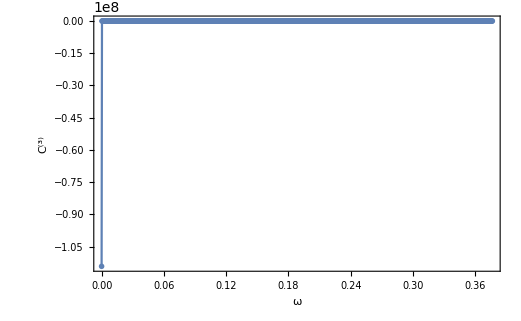

```mathematica
ListPlot[Transpose[{ωL,χ3L}],Frame-> True,Axes-> False,FrameLabel->{"ω","C^(3)","3rd order susceptibility for Si:P"},LabelStyle->{FontSize->20,Bold} ,RotateLabel->False,PlotLegends->Automatic,PlotRange->All,Joined-> True,PlotMarkers->{Style["⋄",Red,FontSize->20]}]
```

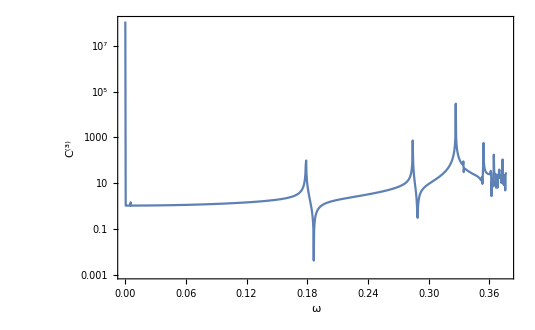

```mathematica
ListLogPlot[Transpose[{ωL,Abs[χ3L]}],Frame-> True,Axes-> False,FrameLabel->{"ω","C^(3)","3rd order susceptibility for Si:P"},LabelStyle->{FontSize->20,Bold} ,RotateLabel->False,PlotLegends->Automatic,PlotRange->All,Joined-> True]
```

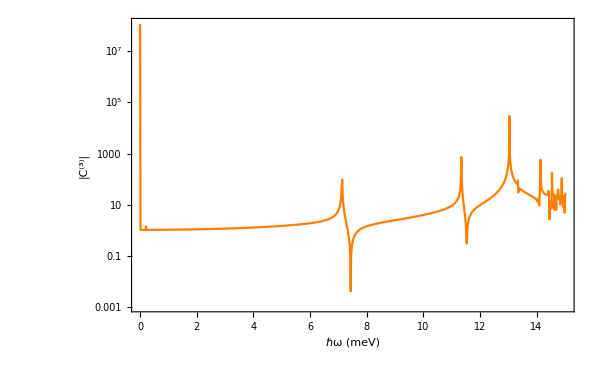

```mathematica
ListLogPlot[Transpose[{ωL*(39.9),Abs[χ3L]}],Frame-> True,Axes-> False,FrameLabel->{"ℏω (meV)","|C^(3)|","3rd order susceptibility, E_B=45.5 meV"},LabelStyle->{FontSize->20,Bold} ,RotateLabel->False,PlotRange->All,Joined-> True,PlotStyle->{Orange}]
```

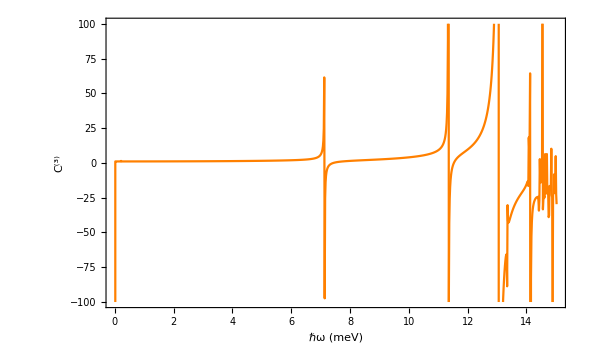

```mathematica
ListPlot[Transpose[{ωL*(39.9),χ3L}],Frame-> True,Axes-> False,FrameLabel->{"ℏω (meV)","C^(3)","3rd order susceptibility, E_B=45.5 meV"},LabelStyle->{FontSize->20,Bold} ,RotateLabel->False,PlotRange->{-100,100},Joined-> True,PlotStyle->{Orange}]
```

```mathematica
DumpSave["chi3SiPMVv4.mx",{ωL,χ3L1,χ3L2,χ3L3,χ3L4,χ3L}];
```